# Energy Spread v Optimised Collimated Flux

```mathematica
(*This code aims to produce a graph of the optimised collimated flux against the energy spread for a fixed 0.5% bandwidth*)
(*This is to try and compare the effects of the bunch length and energy spread to gauge the longitudinal match requirements for an ICS*)
```

## Constants

```mathematica
(*Normal Constants*)
sigT = 6.65*10^-29;
Me = 0.511*10^6;
eleccharge=1.6*10^-19;
lightspeed=299792458;
```

## Cases

```mathematica
(*Cases for trial*)
DIANA1020 = {γ->1996, Elaser->1.17,ϵn->0.5*10^-6,ϕ->0,σL->25*10^-6,Q->100*10^-12,Epulse->100*10^-6,rep->100*10^6,tpulse->5.7*10^-12,σz->3*10^-3,ELSpread->6.57*10^-4};
(*Bunch length is fixed here as we know minimising this is the best for our source*)
DIANA680 = {γ->1331, Elaser->1.17,ϵn->0.5*10^-6,ϕ->0,σL->25*10^-6,Q->100*10^-12,Epulse->100*10^-6,rep->100*10^6,tpulse->5.7*10^-12,σz->3*10^-3,ELSpread->6.57*10^-4};

DIANA340 = {γ->665, Elaser->1.17,ϵn->0.5*10^-6,ϕ->0,σL->25*10^-6,Q->100*10^-12,Epulse->100*10^-6,rep->100*10^6,tpulse->5.7*10^-12,σz->3*10^-3,ELSpread->6.57*10^-4};

(*Select case*)
trialcase=DIANA1020;
```

## Base Equations

```mathematica
(*Recoil Parameter*)
Xrec[γ_,Einc_]:=(4*γ*Einc)/Me;

(*Collimation Parameter*)
ψ[θ_,γ_]:=γ*θ;

(*Compton Cross Section*)
σc[γ_,Einc_]:=sigT*(1-Xrec[γ,Einc]);

(*No. Electrons*)
Ne[Q_]:=Q/eleccharge;

(*No. Photons*)
NL[Epulse_,Einc_]:=Epulse/(Einc*eleccharge);
```

## Equations For Simplification of Main Equations

```mathematica
(*See the images of the derrivation on the google drive for details of these*)
```

```mathematica
B[γ_,Einc_]:=Sqrt[12]*(1+Xrec[γ,Einc]);
P=Sqrt[12]/2;
(*C --> P, C is protected*)
T[γ_,ϵn_]:=2*γ*ϵn;
(*D-->T, D is Protected*)
G[γ_,Einc_,Q_,Epulse_,f_,ϕ_]:=(σc[γ,Einc]*f*Ne[Q]*NL[Epulse,Einc]*Cos[ϕ/2])/(2*π);
H[σz_,tpulse_,ϕ_]:=Sqrt[σz^2+(lightspeed*tpulse)^2]*Sin[ϕ/2]^2;
R[ϕ_]:=Cos[ϕ/2]^2;
(*I-->R, I is Imaginary number*)
J[σL_]:=σL^2;
K[γ_,ϵn_]:=ϵn/γ;
L[γ_,Einc_]:=CubeRoot[Xrec[γ,Einc]]/3;
M[γ_,Einc_]:=1+Xrec[γ,Einc]/2;
V[ELSpread_]:=ELSpread;
Y[γ_,Einc_]:=1+Xrec[γ,Einc];
```

## Optimisation Parameters

```mathematica
(*Fixed Bandwidth Value*) 
BW=0.5*1/100;
(*Energy Spread*)
Ebmin=0;
Ebmax=10^-3;
Ebstep=10^-5;
nEb=IntegerPart[(Ebmax-Ebmin)/Ebstep];
(*Step Limits*)
θtop=5*10^-3;
θbottom = 0;
step=10^-7;
npoints=(θtop-θbottom)/step;
```

## Main Calculation

```mathematica
(*Arrays*)
Arr=Array[f,{nEb,4,npoints}];
Array[endpoint,{nEb}];
```

```mathematica
For[α=0,α<nEb,α++,
EbSpread=Ebmin+α*Ebstep;
For[i=0,i<npoints,i++,
θ=i*step;
β=Sqrt[(T[γ,ϵn]/.trialcase)^2/(BW^2-((ψ[θ,γ]/.trialcase)^4/(((B[γ,Elaser]/.trialcase) +P*(ψ[θ,γ]/.trialcase)^2)^2))-((1+(Y[γ,Elaser]/.trialcase))/((Y[γ,Elaser]/.trialcase)+(ψ[θ,γ]/.trialcase)^2))^2*(EbSpread)^2-((1+(ψ[θ,γ]/.trialcase)^2)/((Y[γ,Elaser]/.trialcase)+(ψ[θ,γ]/.trialcase)^2))^2*(V[ELSpread]/.trialcase)^2)];
(*Break Condition to stop imaginary β*)
If[β==Re[β],
f[α+1,1,i+1]=θ;
f[α+1,2,i+1]=β;
f[α+1,3,i+1]=G[γ,Elaser,Q,Epulse,rep,ϕ]/(Sqrt[K[γ,ϵn]*f[α+1,2,i+1]+J[σL]]*Sqrt[R[ϕ]*(K[γ,ϵn]*f[α+1,2,i+1]+J[σL])+H[σz,tpulse,ϕ]])*(ψ[f[α+1,1,i+1],γ]^2+L[γ,Elaser]*ψ[f[α+1,1,i+1],γ]^4)/(1+(M[γ,Elaser]+1)*ψ[f[α+1,1,i+1],γ]^2+M[γ,Elaser]*ψ[f[α+1,1,i+1],γ]^4)/.trialcase;
(*f[α+1,3,i+1]=(k[γ,Elaser,Q,Epulse,rep]/.trialcase)/(f[α+1,2,i+1]*(g[ϵn,γ]/.trialcase)+(z[σL]/.trialcase))*((ψ[f[α+1,1,i+1],γ]/.trialcase)^2+(h[γ,Elaser]/.trialcase)*(ψ[f[α+1,1,i+1],γ]/.trialcase)^4)/(1+((j[γ,Elaser]/.trialcase)+1)*(ψ[f[α+1,1,i+1],γ]/.trialcase)^2+(j[γ,Elaser]/.trialcase)*(ψ[f[α+1,1,i+1],γ]/.trialcase)^4);*)
f[α+1,4,i+1]=EbSpread;
endpoint[α+1]=i+1;
,
endpoint[α+1]=i;
Break[];
];
];
];
```

## Parameter Space Plotting

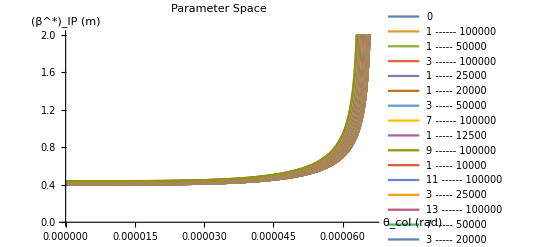

```mathematica
ListLinePlot[Table[Transpose[{Arr[[i,1,All]],Arr[[i,2,All]]}],{i,nEb}],AxesLabel->{"θ_col (rad)","(β^*)_IP (m)"},PlotLabel->"Parameter Space",PerformanceGoal->"Quality",PlotRange->{0,2},PlotLegends->Table[ToString[f[i,4,1]],{i,nEb}]]
```

## Finding F_ψ Maximised Values

```mathematica
(*Storage Arrays*)

(*Eta Array for Subscript[F, ψ] and EbSpread maxes*)
Arr2=Array[η,{2,nEb}];

(*Zeta array for θ and β maxes*)
Arr3=Array[ζ,{2,nEb}];
```

```mathematica
(*Get  Subscript[F^MAX, ψ] θ and β for this maximum EbSpread*)
For[α=0,α<nEb,α++,
maxindex = Position[Arr⟦α+1⟧⟦3⟧,Max[Arr⟦α+1⟧⟦3⟧⟦1;;endpoint[α+1]⟧](*⟦1⟧*)]⟦1,1⟧;
(* EbSpread, Flux, Angle, Beta*)
η[1,α+1]=f[α+1,4,maxindex];
η[2,α+1]=f[α+1,3,maxindex];
ζ[1,α+1]=f[α+1,1,maxindex];
ζ[2,α+1]=f[α+1,2,maxindex];
];
```

## Plotting

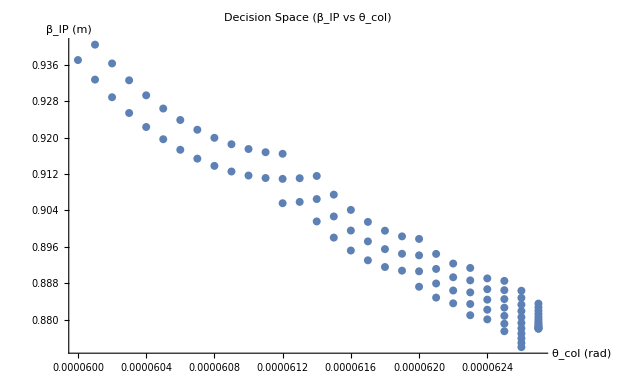

```mathematica
(*Maximum Points in the Parameter Space*)
ListPlot[ Transpose[Arr3],AxesLabel->{"θ_col (rad)","β_IP (m)"},PlotLabel->"Decision Space (β_IP vs θ_col)",PlotRange->All]
```

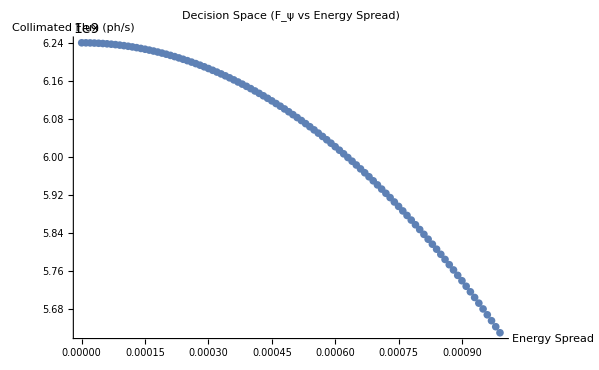

```mathematica
(*Plotting the Decision Space*)
ListPlot[ Transpose[Arr2],AxesLabel->{"Energy Spread","Collimated Flux (ph/s)"},PlotLabel->"Decision Space (F_ψ vs Energy Spread)"]
```

## Saving

```mathematica
SetDirectory[NotebookDirectory[]];
(*Arr2>>"case340FEbSpread.txt"
Arr3>> "case340BetaThetaEbSpread.txt"*)
```

## Multiple Energy Plot

```mathematica
SetDirectory[NotebookDirectory[]];
DIANAβθ1020=<<"case1020BetaThetaEbSpread.txt";
DIANAβθ680=<<"case680BetaThetaEbSpread.txt";
DIANAβθ340=<<"case340BetaThetaEbSpread.txt";
```

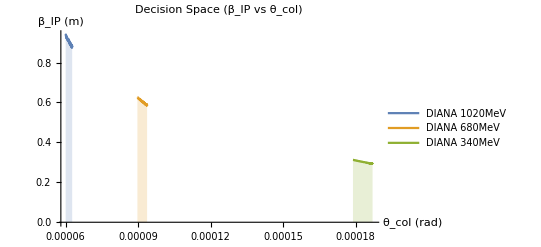

```mathematica
(*Plot*)
ListLinePlot[{Transpose[DIANAβθ1020],Transpose[DIANAβθ680],Transpose[DIANAβθ340]},AxesLabel->{"θ_col (rad)","β_IP (m)"},PlotLabel->"Decision Space (β_IP vs θ_col)",PlotLegends->{"DIANA 1020MeV","DIANA 680MeV","DIANA 340MeV"},PlotRange->All,Filling->Axis]
```

```mathematica
(*Using Multiple Cases to create Subscript[F, ψ]-BW plots*)
SetDirectory[NotebookDirectory[]];
DIANAFEb1020=<<"case1020FEbSpread.txt";
DIANAFEb680=<<"case680FEbSpread.txt";
DIANAFEb340=<<"case340FEbSpread.txt";
```

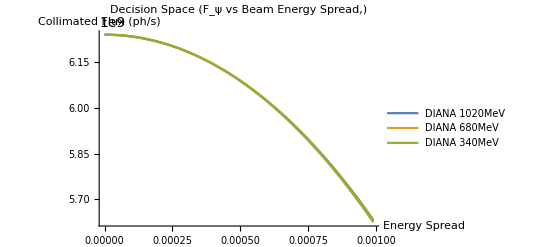

```mathematica
(*Plot*)
ListLinePlot[{Transpose[DIANAFEb1020],Transpose[DIANAFEb680],Transpose[DIANAFEb340]},AxesLabel->{"Energy Spread","Collimated Flux (ph/s)"},PlotLabel->"Decision Space (F_ψ vs Beam Energy Spread,)",PlotLegends->{"DIANA 1020MeV","DIANA 680MeV","DIANA 340MeV"}]
```